# xlr8r example

## Circadian Oscillator Model

Created: 11 October 2005 BES
Revised: 15 Oct 2007 BES - verify under Version 6.0

#### References

Vilar JMG, Kueh HY, Barkai N, Leibler S, (2002) "Mechanisms of noise resistance in genetic oscillators," PNAS, 99(9):5988-5992.
Barkai N, Leibler S (2000)  "Circadian clocks limited by noise," Nature, 403:267-268.

```mathematica
<<xlr8r.m
```

xlr8r 0.60 (15-Oct-2007) loaded 15-October-2007 13:19:09.864148 using Mathematica 6.0 for Mac OS X x86 (32-bit) (June 19, 2007)

## Define the Reaction Network

```mathematica
STN  ={{A+R->C, γC}, 
{A->∅,δA},
{C->R,δA},
{R->∅,δR},
{A+DA⇄DAp, γA,θA},
{DA->DA+MA,αA},
{DAp->DAp+MA,αAp},
{MA->∅,δMA},
{MA->MA+A,βA},
{A+DR⇄DRp,γR,θR},
{DR->DR+MR,αR},
{DRp->DRp+MR,αRp},
{MR->∅,δMR},
{MR->MR+R,βR}
};
```

## Generate Differential Equations

```mathematica
s=interpret[STN]
```

{{A'[t]==-δA A[t]-γA A[t] DA[t]+θA DAp[t]-γR A[t] DR[t]+θR DRp[t]+βA MA[t]-γC A[t] R[t],C'[t]==-δA C[t]+γC A[t] R[t],DA'[t]==-γA A[t] DA[t]+θA DAp[t],DAp'[t]==γA A[t] DA[t]-θA DAp[t],DR'[t]==-γR A[t] DR[t]+θR DRp[t],DRp'[t]==γR A[t] DR[t]-θR DRp[t],MA'[t]==αA DA[t]+αAp DAp[t]-δMA MA[t],MR'[t]==αR DR[t]+αRp DRp[t]-δMR MR[t],R'[t]==δA C[t]+βR MR[t]-δR R[t]-γC A[t] R[t]},{A,C,DA,DAp,DR,DRp,MA,MR,R}}

## Define Rate Constants

```mathematica
RateConstants={γC-> 2,δA-> 1,δR-> 0.2,γA-> 1,θA-> 50,
αA-> 50,αAp-> 500,γR-> 1,θR-> 100,αR-> 0.01,αRp-> 50,δMA-> 10,δMR-> 0.5,βA-> 50,βR-> 5};
```

## Define InitialConditions

```mathematica
STNInitialConditions = {DR-> 1, DA-> 1};
```

## Predict a time course (run a single simulation)

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {A,C,DAp,DRp,MA,MR,R}

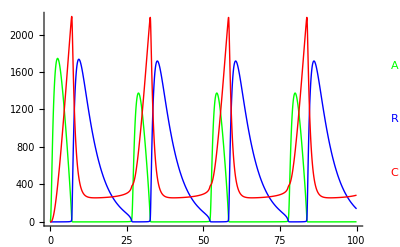

{{A→InterpolatingFunction[{{0.,100.}},<>],C→InterpolatingFunction[{{0.,100.}},<>],DA→InterpolatingFunction[{{0.,100.}},<>],DAp→InterpolatingFunction[{{0.,100.}},<>],DR→InterpolatingFunction[{{0.,100.}},<>],DRp→InterpolatingFunction[{{0.,100.}},<>],MA→InterpolatingFunction[{{0.,100.}},<>],MR→InterpolatingFunction[{{0.,100.}},<>],R→InterpolatingFunction[{{0.,100.}},<>]}}

```mathematica
sim=run[STN,
initialConditions->STNInitialConditions,
rates-> RateConstants,
timeSpan->100,
MaxSteps->25000, 
plot-> True,
plotVariables-> {A,R,C}]
```

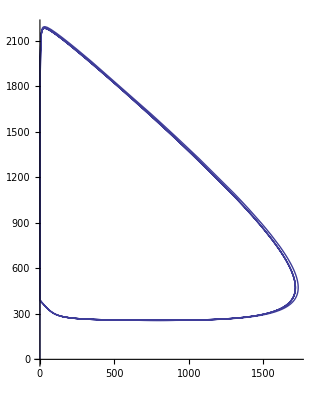

```mathematica
ParametricPlot[{R[t],C[t]}/.sim, {t,0,100}]
```